```mathematica
csvPath = "M:\\JI Courses\\Sophomore_Year\\2019_Spring\\VE401\\Proj2\\Figures\\2\\data.csv";
SystemOpen@csvPath
Data = Import[csvPath];
PosDate = Position[Data,"2019-01-01"];
AllDate = Data[[2;;PosDate[[1,1]]-1,PosDate[[1,2]];;PosDate[[1,2]]]];
For[i=1,i<=Length[AllDate],i++,AllDate[[i]]=DayName[DateObject[StringCases[AllDate[[i,1]],x:DatePattern[{"Year","Month","Day"}]:>DateList[x]][[1;;1,1;;3]]]]];
Count1=Tally[AllDate]
```

{{{Friday},572},{{Saturday},518},{{Sunday},561},{{Monday},517},{{Tuesday},586},{{Wednesday},616},{{Thursday},573}}

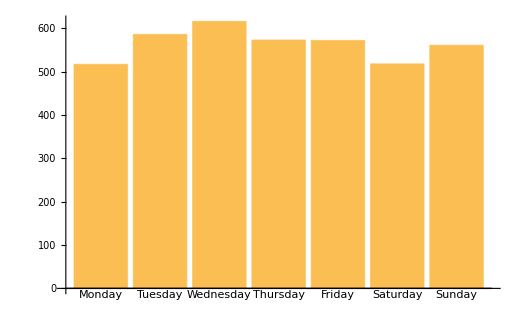

```mathematica
(*Adjust the Orders and make the barchart*)
Count1={{Monday,517},{Tuesday,586},{Wednesday,616},{Thursday,573},{Friday,572},{Saturday,518},{Sunday,561}};
Count2=Count1[[All,1]];
Count3=Count1[[All,2]];
BarChart[Count3,ChartLabels->Count2]
```

```mathematica
(*The following appies Pearson's Goodness-of-fit to test dependece of shotting and days, the latter part is in excel file*)
```

```mathematica
AllShoot=Length[AllDate]
AvgShoot=N[AllShoot/(365*4+1)]
Count4=Count3;
Count4[[1]]=N[Count3[[1]]/209];
Count4[[2]]=N[Count3[[2]]/208];
Count4[[3]]=N[Count3[[3]]/208];
For[i=4,i≤7,i++,Count4[[i]]=N[Count3[[i]]/209]];
Count3
```

3943

2.69884

{2.47368,2.81731,2.96154,2.74163,2.73684,2.47847,2.68421}